# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Channels

# Interacting two qubits

```mathematica
PauliMatrix[0]//MatrixForm
PauliMatrix[1]//MatrixForm
PauliMatrix[2]//MatrixForm
PauliMatrix[3]//MatrixForm
```

(1 | 0
0 | 1)

(0 | 1
1 | 0)

(0 | -ⅈ
ⅈ | 0)

(1 | 0
0 | -1)

```mathematica
Clear[ham];
ham[a_,b_,c_]:=a*(KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+KroneckerProduct[PauliMatrix[2],PauliMatrix[0]]+KroneckerProduct[PauliMatrix[1],PauliMatrix[0]])+b*(KroneckerProduct[PauliMatrix[0],PauliMatrix[3]]+KroneckerProduct[PauliMatrix[0],PauliMatrix[2]]+KroneckerProduct[PauliMatrix[0],PauliMatrix[1]])+c*KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]+ConjugateTranspose[a*(KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+KroneckerProduct[PauliMatrix[2],PauliMatrix[0]]+KroneckerProduct[PauliMatrix[1],PauliMatrix[0]])+b*(KroneckerProduct[PauliMatrix[0],PauliMatrix[3]]+KroneckerProduct[PauliMatrix[0],PauliMatrix[2]]+KroneckerProduct[PauliMatrix[0],PauliMatrix[1]])]
```

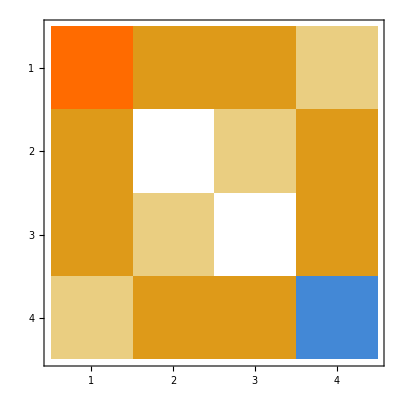

```mathematica
ham[1,1,1]//MatrixPlot
```

```mathematica
a=1;
b=1;
c=10;
h=ham[a,b,c];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[h]]]]];
```

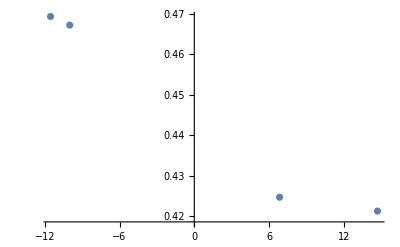

```mathematica
ListPlot[Transpose[{eigenval,iprs}]]
```

```mathematica
Clear[u];
u[t_]:=MatrixExp[-I*t*h];
```

```mathematica
evol1=Table[u[t].{1,0,0,0},{t,0,5,0.1}];
evol2=Table[u[t].{0,1,0,0},{t,0,5,0.1}];
evol3=Table[u[t].{0,0,1,0},{t,0,5,0.1}];
evol4=Table[u[t].{0,0,0,1},{t,0,5,0.1}];
evol5=Table[u[t].Flatten[KroneckerProduct[Normalize[{RandomReal[],RandomReal[]}],{1,0}]],{t,0,5,0.1}];
```

```mathematica
sp1=Table[Abs[Conjugate[evol1[[1]]].evol1[[i]]]^2,{i,Length[evol]}];
sp2=Table[Abs[Conjugate[evol2[[1]]].evol2[[i]]]^2,{i,Length[evol]}];
sp3=Table[Abs[Conjugate[evol3[[1]]].evol3[[i]]]^2,{i,Length[evol]}];
sp4=Table[Abs[Conjugate[evol4[[1]]].evol4[[i]]]^2,{i,Length[evol]}];
sp5=Table[Abs[Conjugate[evol5[[1]]].evol5[[i]]]^2,{i,Length[evol]}];
```

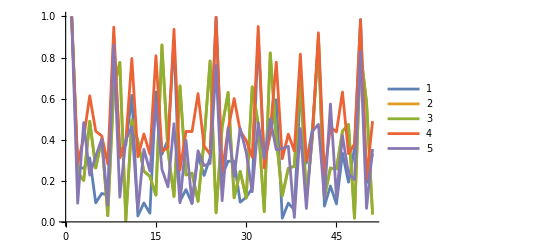

```mathematica
ListPlot[{sp1,sp2,sp3,sp4,sp5},PlotRange->All,Joined->True,PlotLegends->Automatic]
```

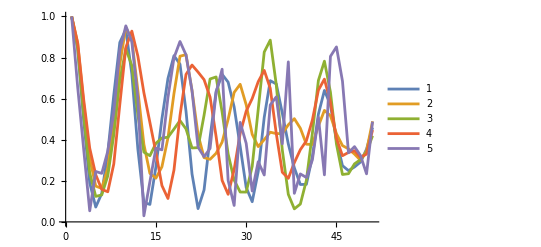

```mathematica
ListPlot[{sp1,sp2,sp3,sp4,sp5},PlotRange->All,Joined->True,PlotLegends->Automatic]
```

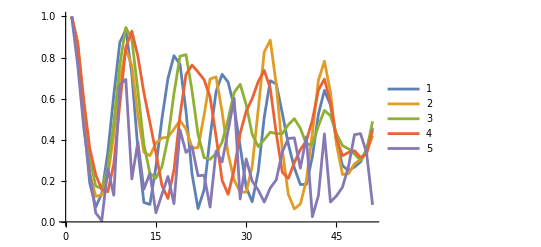

```mathematica
ListPlot[{sp1,sp2,sp3,sp4,sp5},PlotRange->All,Joined->True,PlotLegends->Automatic]
```

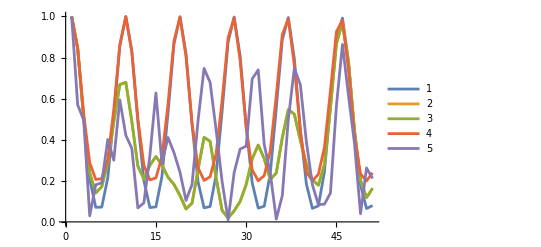

```mathematica
ListPlot[{sp1,sp2,sp3,sp4,sp5},PlotRange->All,Joined->True,PlotLegends->Automatic]
```